# Fully implicit scheme for normal pulse voltammetry

## with Richtmyer modification and expanding space grid.

Version 2.0
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.7]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
(*options for voltammograms*)

optionA={
FrameTicks-> Automatic,
PlotStyle->{Red,AbsoluteThickness[0.7]},
FrameLabel->{
Style["increment",FontFamily->"Arial" ,FontSize-> 12,FontColor->Black],
Style["χ",FontFamily-> "Times New Roman" ,FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None}
};
```

```mathematica
(*options for voltammograms*)

optionB={
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameTicks-> Automatic,
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontColor-> Black,FontSlant-> Italic,FontSize-> 12],
Style["χ",FontFamily-> "Times New Roman",FontSlant-> Italic,FontColor->Black,FontSize-> 12],
None,
None}
};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeVarDiagonals2];

makeVarDiagonals2[m_Integer,d_][a_]:=
	Module[{x,y,z},
		x=Table[-d*a^(4-2*j),{j,3,m-1}];(*lower diagonal*)
		z=Table[-d*a^(3-2*j),{j,2,m-2}];(*upper diagonal*)
		y=Table[1+(1+a)*d*a^(3-2*j),{j,2,m-1}];(*centre*)
{x,y,z}]

Clear[makeRichtmyerExpDiagonals];

makeRichtmyerExpDiagonals[m_Integer,d_][a_]:=Module[{x,y,z},
		x=Table[-d*a^(4-2*j),{j,3,m-1}];
		z=Table[-d*a^(3-2*j),{j,2,m-2}];
		y=Table[(25./12.+(1.+a)*d*a^(3-2*j)),{j,2,m-1}];
{x,y,z}]
```

## Set Up Solution

```mathematica
Clear[implicitExpNP];

implicitExpNP[m_Integer,n_Integer,d_,{upperLimit_,ksStar_,α_,Δ𝔼p_,tL_,p_},a_]:=Module[{x,y,z,len,mat,y1,z1,initial,solveNext},

{x,y,z}=makeVarDiagonals2[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2,u},
u[j_]=UnitStep[(j-tL+p)(j-tL)(j-tL-100)];

ξ=Exp[upperLimit-Δ𝔼p*Ceiling[k/tL]*u[Mod[k,tL]]];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=list[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦m-2⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]
];
FoldList[solveNext,initial,Range[0,n]]
]
```

```mathematica
Clear[implicitExpRichtmeyerNP];

implicitExpRichtmeyerNP[m_Integer,n_Integer,d_,{upperLimit_,ksStar_,α_,Δ𝔼p_,tL_,p_},a_]:=Module[{x,y,z,len,mat,y1,z1,initial,c,solveStart,solveRest},

{x,y,z}=makeVarDiagonals2[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveStart[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2,u},
u[j_]=UnitStep[(j-tL+p)(j-tL)(j-tL-100)];

ξ=Exp[upperLimit-Δ𝔼p*Ceiling[k/tL]*u[Mod[k,tL]]];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=list[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦m-2⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]
];
c=FoldList[solveStart,initial,Range[0,5]];

{x,y,z}=makeRichtmyerExpDiagonals[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;

solveRest[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2,u},
u[j_]=UnitStep[(j-tL+p)(j-tL)(j-tL-100)];

ξ=Exp[upperLimit-Δ𝔼p*Ceiling[k/tL]*u[Mod[k,tL]]];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=Flatten@MapThread[{4*#4-3*#3+(4./3.)*#2-0.25*#1}&,Take[list,-4]];
b=b⟦2;;-2⟧;
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦-1⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
Join[list,{Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]}]
];

Fold[solveRest,c,Range[6,n]]
]
```

```mathematica
Clear[implicitExpNPP];

implicitExpNPP[m_Integer,n_Integer,d_,{upperLimit_,ksStar_,α_,Δ𝔼p_,tL_,p_},a_]:=Module[{x,y,z,len,mat,y1,z1,initial,solveNext,normalPolar,conc},

{x,y,z}=makeVarDiagonals2[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveNext[k_][list_,int_]:=Module[{tmp,b,tmp2,ξ},
ξ=Exp[upperLimit-Δ𝔼p*k];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=conc[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦m-2⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
conc=Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}];
Take[conc,3]
];

normalPolar[list2_,j_]:=Module[{temp},
temp=Rest[FoldList[solveNext[j],conc,Range[0,p-1]]];
conc=initial;
temp];

conc=initial;
conc=Rest@FoldList[normalPolar,conc,Range[1,pulses]];
Partition[Flatten[conc],3]
]
```

## Set Parameter Values

### Variables/ constants

```mathematica
Clear[F,R,T,f,𝒟];

F=N@QuantityMagnitude[UnitConvert@Quantity["FaradayConstant"]];(*Faradays constant*)

R=N@QuantityMagnitude[UnitConvert@Quantity["GasConstant"]];(*gas constant*)

T=298.15;(*temperature*)
f=F/(R*T);
𝒟=1.*^-5;(*diffusion coefficient*)
```

### Electrochemical variables

```mathematica
Clear[α,ks,Δ𝔼p,upperLimit,𝕥];

α=0.5; (*transfer coefficient*)

ks=1.*^3;(*dimensionless standard rate constant*)

Δ𝔼p=f*0.005;(*dimensionless normal pulse step size*)

upperLimit=10.;(*initial potential versus the formal potential*)

𝕥=20.;(*approximate range required*)
```

### Simulation variables

```mathematica
Clear[𝔻,pulses,p,tL,n,a,temp,m,τ,ksStar];

𝔻=2.;(*model diffusion coefficient*)

pulses=Round[𝕥/Δ𝔼p];(*number of pulses*)

p=5;(*length of the pulse*)

tL=100;(*length of pulse plus length of rest time*)

n=pulses*tL;

a=1.1;(*grid expansion factor*)

temp=Solve[∑_(j=1)^(mm-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),mm,InverseFunctions-> True];

m=Ceiling[mm/.temp⟦1⟧];(*number of spacial grid points*)


τ=𝕥/n; (*calculation of the incremental potential step*)

ksStar=2.ks*Sqrt[1./(Pi*𝔻*(p-1))];(*dimensionless rate constant*)
```

```mathematica
{α,ks,Δ𝔼p,upperLimit,𝕥,𝔻,pulses,p,tL,n,a,m,τ,ksStar}
```

{0.5,1000.,0.194609,10.,20.,2.,103,5,50,5150,1.1,45,0.0038835,398.942}

## Show waveform

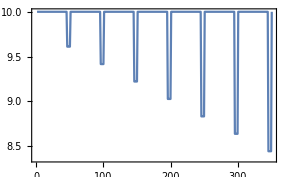

```mathematica
u[j_]:=UnitStep[(j-tL+p)(j-tL)(j-tL-100)];

normPulse=Table[upperLimit-Δ𝔼p*Ceiling[k/tL]*u[Mod[k,tL]],{k,50,400}];

ListPlot[normPulse]
```

## Fully implicit normal pulse voltammogram

For a fully implicit solution execute the cell below:

```mathematica
c=implicitExpNP[m,n,𝔻,{upperLimit,ksStar,α,Δ𝔼p,tL,p},a];
```

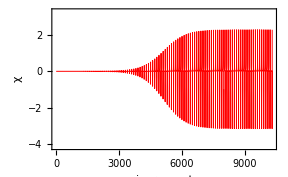

```mathematica
npv1=Map[(((2.+a)*a*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)*√((Pi*𝔻*(p-1))/(2.*a^2*(1.+a))))&,c];

plot1=ListPlot[npv1,optionA,PlotRange-> {{0,n},{Min[npv1]-1,Max[npv1]+1}}]
```

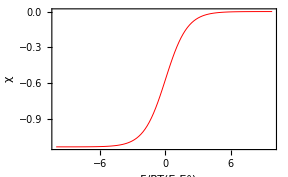

```mathematica
normal=Table[{upperLimit-(k*Δ𝔼p/tL),npv1⟦k⟧},{k,tL,Length[npv1],tL}];

normalPlot=ListPlot[normal,optionB,PlotStyle-> {Red}]
```

```mathematica
Min[normal⟦All,2⟧]
```

-1.13394

The expected minimum is -1. Close but no cigar. A longer resting time (larger tL) is needed since in the theory which predicts a height of ±1 at the top of the step assumes that the concentration profile at the beginning of a pulse is what it was at the start of the experiment. Richtmyer modification may offer some improvement.

## FIRM normal pulse voltammogram

For a fully implicit solution with Richtmyer modification execute the cell below:

```mathematica
c=implicitExpRichtmeyerNP[m,n,𝔻,{upperLimit,ksStar,α,Δ𝔼p,tL,p},a];//Timing
```

{9.92992,Null}

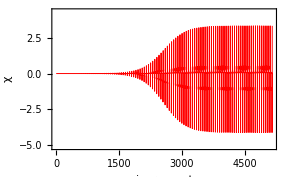

```mathematica
npv1=Map[(((2.+a)*a*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)*√((Pi*𝔻*(p-1))/(2.*a^2*(1.+a))))&,c];

plot1=ListPlot[npv1,optionA,PlotRange-> {{0,n},{Min[npv1]-1,Max[npv1]+1}}]
```

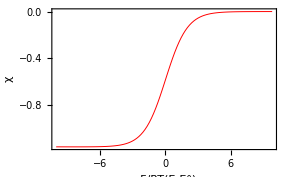

```mathematica
normal=Table[{upperLimit-(k*Δ𝔼p/tL),npv1⟦k⟧},{k,tL,Length[npv1],tL}];

normalPlot=ListPlot[normal,optionB,PlotStyle-> {Red}]
```

```mathematica
Min[normal⟦All,2⟧]
```

-1.1587

The expected minimum is -1. Close but no cigar. A longer resting time (larger tL) is needed since in the theory which predicts a height of ±1 at the top of the step assumes that the concentration profile at the beginning of a pulse is what it was at the start of the experiment. Richtmyer modification may offer some improvement.

## Normal pulse polarogram

This next method is for normal pulse polarography. The assumption is that the concentrations are at the bulk values prior to each pulse.

```mathematica
cNP=implicitExpNPP[m,n,𝔻,{upperLimit,ksStar,α,Δ𝔼p,tL,p},a];
```

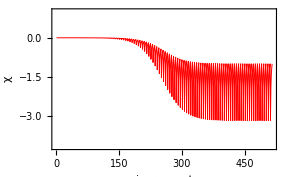

```mathematica
Clear[npv2]

npv2=Map[(((2.+a)*a*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)*√((Pi*𝔻*(p-1))/(2.*a^2*(1.+a))))&,cNP];

plot1=ListPlot[npv2,optionA,PlotRange-> {{0,Length[cNP]},{Min[npv2]-1,Max[npv2]+1}}]
```

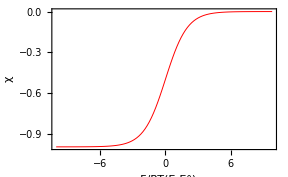

```mathematica
normalPolarography=Table[{upperLimit-(Δ𝔼p*k/p),npv2⟦k⟧},{k,p,Length[npv2],p}];

normalPlot2=ListPlot[normalPolarography,PlotRange->All,optionB,PlotStyle-> {Red}]
```

```mathematica
Min[normalPolarography⟦All,2⟧]
```

-0.994047